```mathematica
NN = 3
```

3

```mathematica
maxr = 100
maxk = 100
CMSz[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]]∑_(r=1)^maxr NN/(r NN + 1)( 1 - 1/(1 - a))^r
CMSzsimple[a_] := Exp[1/NN Log[a]]/Exp[1/NN ⅈ π] a
CMSzsimple1[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]] a
```

100

100

```mathematica
m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := (- 1)/(2π)( NN σ0[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ])



W1[a_] := -1/(2π) (NN σ1[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ] )



CMS[a_] := (- NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) - ∑_(j=0)^(NN-1) mj[a,j] ( Log[ σ1[a] - mj[a,j] ] - Log [ σ0[a] - mj[a,j] ] ))/(m1[a] - m0[a])

CMSFrac[a_, q1_, q2_] := CMS[a]  +  2 π ⅈ q1  +  (2 π ⅈ q2 ( mj[a,2] - m0[a] ))/(m1[a] - m0[a])



CMSleft[a_] := CMSFrac[a, -1/3, -1/3]




CMSright[a_] := CMSFrac[a, +1/3, +1/3]


CMSFrac2[a_,s_,q1_] := (W1[a] - W0[a]  +  ⅈ ( s + q1 ) ( m1[a] - m0[a] ))/(mj[a,2] - m0[a])


CMSE[a_] :=  (- NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) - ∑_(j=0)^(NN-1) mj[a,j] ( Log[ 1 - mj[a,j]/σ1[a] ] - Log [ 1 - mj[a,j]/σ0[a] ] ))/(m1[a] - m0[a])
CMSm[a_] := - NN σ0[a]/m0[a]( 1 - ∑_(k=1)^maxk (a/(1 + a))^k/(k NN - 1) )
CMSmN[a_] := - NN σ0[a]/m0[a]( 1 + 1/NN Log [ 1/(1 + a)] )
```

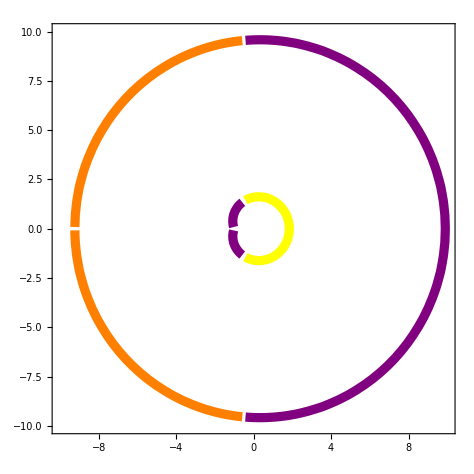

```mathematica
ContourPlot[   { Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0 }, 
                             { x , -10, 10}, { y, -10, 10 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ], 
                                                             Directive[ Thickness[0.014], Orange ] }   ]
```

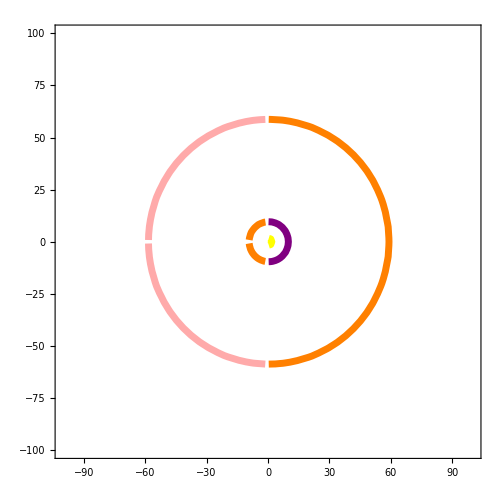

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0,
			   Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 },
                             { x , -100, 100}, { y, -100, 100 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ]  }   ]
```

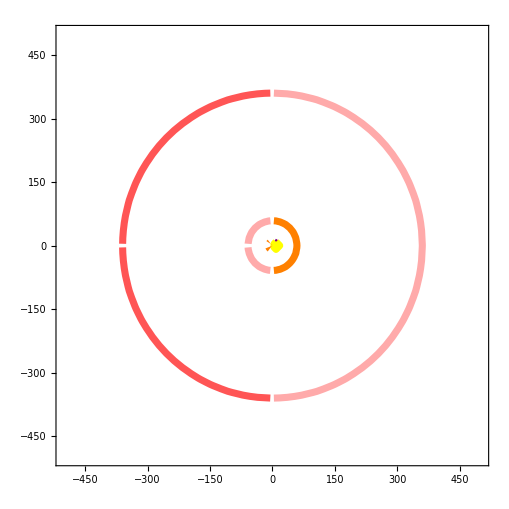

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0,
			 Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 ,
			 Re[CMSright[x + ⅈ y] - 2(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0},
                             { x , -500, 500}, { y, -500, 500 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ],
						    Directive[ Thickness[0.01], Lighter[Red]]  }   ]
```

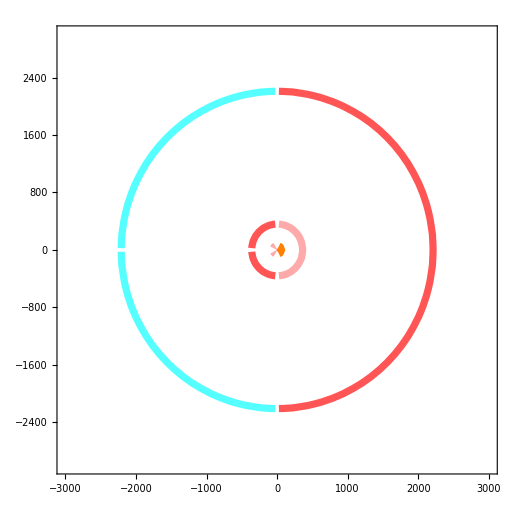

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		           Re[CMSleft[x + ⅈ y]] == 0,
		           Re[CMSright[x + ⅈ y]] == 0,
		           Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 ,
		           Re[CMSright[x + ⅈ y] - 2(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0,
                              Re[CMSright[x + ⅈ y] - 3(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0  },
                             { x , -3000, 3000}, { y, -3000, 3000 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ],
						    Directive[ Thickness[0.01], Lighter[Red]],
                                                             Directive[ Thickness[0.01], Lighter[Cyan]]   }   ]
```

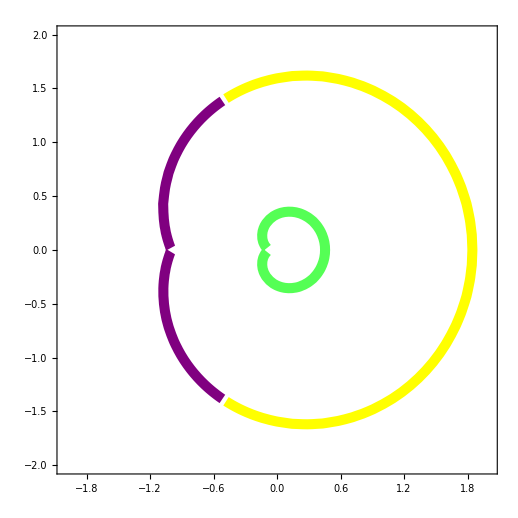

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0 }, 
                             { x , -2, 2 }, { y, -2,2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ] }   ]
```

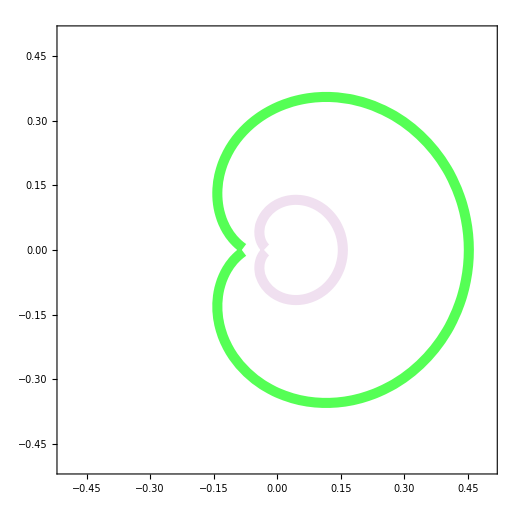

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-3/3,-3/3] ] == 0  }, 
                             { x , -0.5, 0.5 }, { y, -0.5,0.5 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ],
						    Directive[ Thickness[0.014], LightPurple] }   ]
```

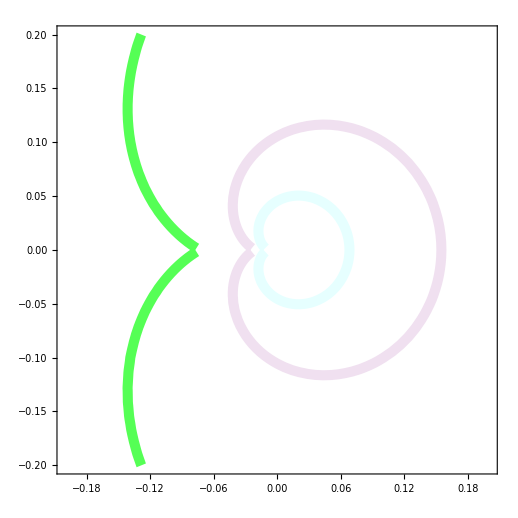

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-3/3,-3/3] ] == 0 ,
			Re[ CMSFrac[x + ⅈ y,-4/3,-4/3] ] == 0 }, 
                             { x , -0.2, 0.2 }, { y, -0.2,0.2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ],
						    Directive[ Thickness[0.014], LightPurple],
						    Directive[ Thickness[0.014], LightCyan] }   ]
```

```mathematica
CMSTower1[a_] := ((ⅇ^(2π ⅈ /3) - 1) W0[a] + ⅈ m0[a])/(m1[a] - m0[a])
CMSTower2[a_] := ((ⅇ^(2π ⅈ /3) - 1) W0[a] + ⅈ mj[a,2])/(m1[a] - m0[a])
```

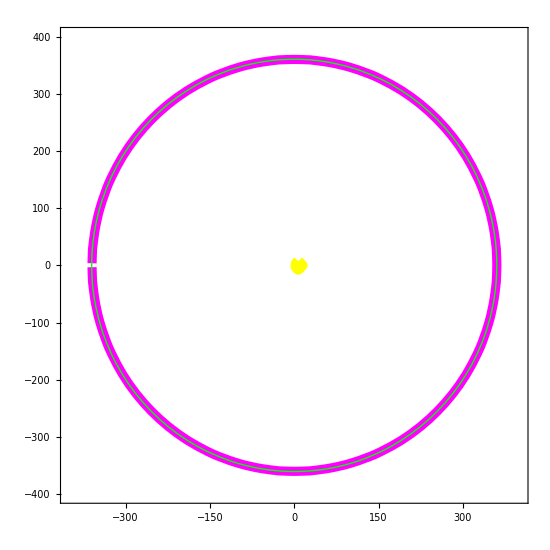

```mathematica
ContourPlot[   { Re[ CMSTower1[x + ⅈ y]] == 0,
		          Re[ CMSTower2[x + ⅈ y]] == 0 ,
			x^2 + y^2 == (360.50440685990253)^2}, 
                            { x , -400, 400}, { y, -400, 400 },
                             ContourStyle->{ Directive[ Thickness[0.014], Yellow ],
                                                             Directive[Thickness[0.012],Magenta],
						    Directive[Green] } ]
```

```mathematica
CMSTower1Left[a_] := (W1[a] - W0[a])/(m1[a] - m0[a])
CMSTower2Left[a_] := (W1[a] - W0[a] + ⅈ ( mj[a,2] - m0[a] ))/(m1[a] - m0[a])
CMSTower1Right[a_] := (W1[a] - W0[a]  + ⅈ m0[a])/(m1[a] - m0[a])
CMSTower2Right[a_] := (W1[a] - W0[a]  + ⅈ mj[a,2])/(m1[a] - m0[a])
```

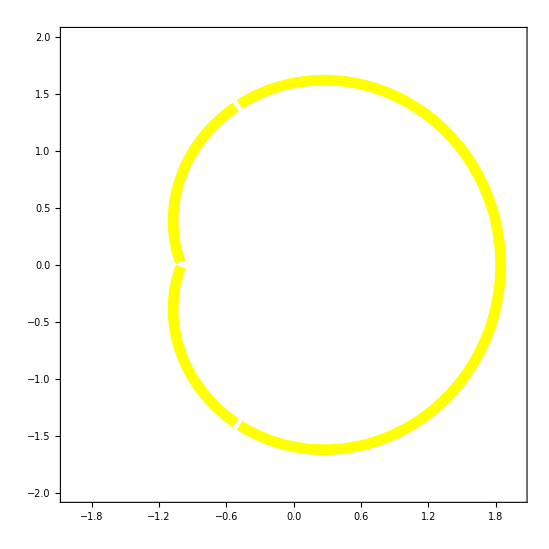

```mathematica
ContourPlot[   { Re[ CMSTower1Left[x + ⅈ y]] == 0,
		          Re[ CMSTower2Left[x + ⅈ y]] == 0,
                             Re[ CMSTower1Right[x + ⅈ y]] == 0,
		          Re[ CMSTower2Right[x + ⅈ y]] == 0 }, 
                            { x , -2, 2}, { y, -2, 2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Yellow ],
                                                             Directive[ Thickness[0.014], Magenta],
                                                             Directive[ Thickness[0.014], Yellow ],
                                                             Directive[ Thickness[0.014], Magenta]  } ]
```

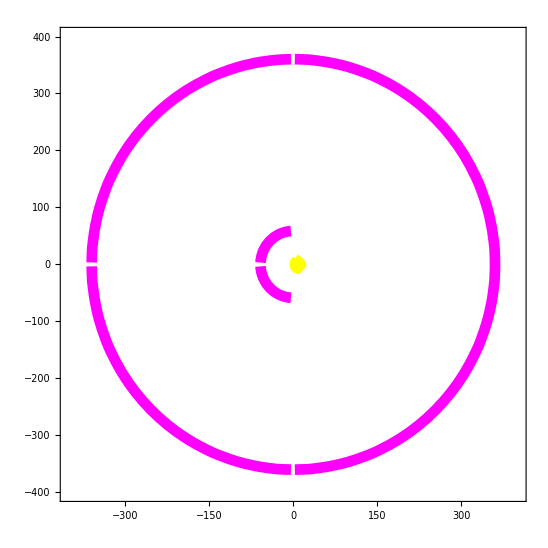

```mathematica
ContourPlot[   { Re[ CMSTower1Left[x + ⅈ y]] == 0,
		          Re[ CMSTower2Left[x + ⅈ y]] == 0,
                             Re[ CMSTower1Right[x + ⅈ y]] == 0,
		          Re[ CMSTower2Right[x + ⅈ y]] == 0 }, 
                            { x , -400, 400}, { y, -400, 400 },
                             ContourStyle->{ Directive[ Thickness[0.014], Yellow ],
                                                             Directive[ Thickness[0.014], Magenta],
                                                             Directive[ Thickness[0.014], Yellow ],
                                                             Directive[ Thickness[0.014], Magenta]  } ]
```

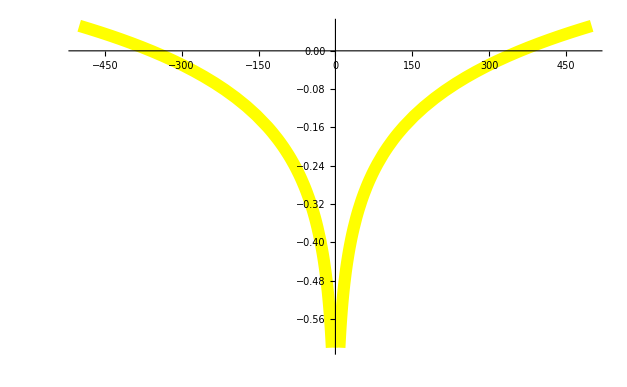

```mathematica
Plot[ {  Re[ CMSTower2[x]] }, {x, -500, 500}, PlotStyle->Directive[ Thickness[0.014], Yellow ] ]
```

```mathematica
FindRoot[ {Re[CMSTower2[x]]},{x,200.}]
```

{x→360.504}